In all calculations the length is in Angstrom and energy in eV.

   m_e = 0.511 MeV/c^2 = 0.0567778 *10^-30 (eV s^2)/A^2 
ℏ^2/m_e= (6.58*10^-16 eV (s))^2/(0.0567*10^-30 (eV s^2)/A^2) = 7.62559 eV A^2

## Even and Odd states using parity conditions:

{0.111146,0.0298714}

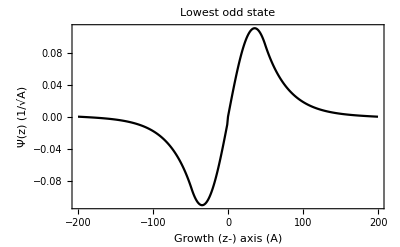

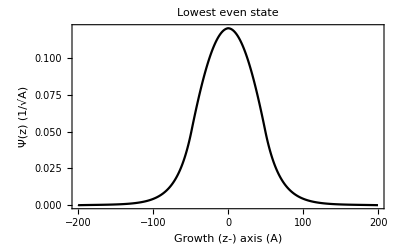

```mathematica
ClearAll["Global`*"]
plots={0.,0.};
energy={0.,0.};
titles = {"Lowest odd state","Lowest even state"};

x=0.2;
hom=7.62559/0.067;(*ℏ^2/m^* for GaAs in eV A^2*)
vmax=0.67*1.247x; (*Diff in conduction band between GaAs and Subscript[Ga, 1-x] Subscript[Al, x] As*)
dz=1.;zmin=-200.;zmax=200.;
z=Range[zmin,zmax,dz];lz=Length[z];i0=(Length[z]+1.)/2.;
ψ=0.*z;v=ConstantArray[vmax,Length[z]];
bw=150.; (*width of the barrier*)
Do[If[z⟦i⟧-z⟦1⟧>bw&&z⟦-1⟧-z⟦i⟧>bw,v⟦i⟧=0.],{i,1,Length[z]}]
c=-0.5*hom/dz^2;b=hom/dz^2+v;
ψmax=2;

(*Loops once for the odd state then once for the even state*)
Do[
ϵ=0.0;dϵ=0.03;
ψ=0.*z;
(* Initialization for shooting written in the form { {Subscript[odd, i0],Subscript[odd, i0+1]} , {Subscript[even, i0],Subscript[even, i0+1]} } *)
ψ⟦{i0,i0+1}⟧={ {0.,0.0001} , {1.,1.+dz^2/hom (v⟦i0⟧-ϵ)} }⟦k⟧;
(*Shooting for zero energy*)
i=i0+1;ψl=ψ⟦i⟧;
While[Abs[ψ⟦i⟧]<ψmax&&i<lz,ψ⟦i+1⟧=1/c (ϵ-b⟦i⟧)ψ⟦i⟧-ψ⟦i-1⟧;i++];
ψl=ψ⟦i⟧;ϵ+=dϵ;

While[Abs[dϵ]>0.0000001,
ψ=0.*z;ψ⟦{i0,i0+1}⟧={ {0.,0.0001} , {1.,1.+dz^2/hom (v⟦i0⟧-ϵ)} }⟦k⟧;
i=i0+1;
While[Abs[ψ⟦i⟧]<ψmax&&i<lz,
ψ⟦i+1⟧=1/c (ϵ-b⟦i⟧)ψ⟦i⟧-ψ⟦i-1⟧;ψ⟦lz-i+1⟧=(-1)^k ψ⟦i+1⟧;i++];(*(-1)^k is due to the parity of the even and odd state*)
If[ψ⟦i⟧*ψl<0,dϵ=-dϵ/2.];
ψl=ψ⟦i⟧;ϵ+=dϵ];
energy⟦k⟧=ϵ-dϵ;(*dϵ is subtracted to account for a final dϵ added while exiting the while loop*)
ψ=ψ/(√(ψ.ψ dz));
plots⟦k⟧=ListLinePlot[Table[{z⟦i⟧,ψ⟦i⟧},{i,1,lz}],PlotStyle->Black,Frame->True, FrameLabel->{"Growth (z-) axis (A)","Ψ(z) (1/√A)"},PlotLabel->titles⟦k⟧]
,{k,2}]

energy
plots⟦1⟧
plots⟦2⟧
```

## Ground state and first excited state using generalized initial conditions:

```mathematica
ClearAll["Global`*"]
plots={0.,0.};
energy={0.,0.,0.};
titles = {"Ground state (Generalised conditions)","First excited state (Generalised conditions)"};

x=0.2;
hom=7.62559/0.067;(*ℏ^2/m^* in eV A^2*)
vmax=0.67*1.247x; (*Diff in conduction band between GaAs and Subscript[Ga, 1-x] Subscript[Al, x] As*)
dz=1.;zmin=-200.;zmax=200.;
z=Range[zmin,zmax,dz];lz=Length[z];i0=(Length[z]+1.)/2.;
ψ=0.*z;v=ConstantArray[vmax,Length[z]];
bw=150.; (*width of the barrier*)
Do[If[z⟦i⟧-z⟦1⟧>bw&&z⟦-1⟧-z⟦i⟧>bw,v⟦i⟧=0.],{i,1,Length[z]}]
c=-0.5*hom/dz^2;b=hom/dz^2+v;
ψmax=2;
Do[
ϵ=energy⟦k⟧+0.01;dϵ=0.03;
ψ=0.*z;ψ⟦{1,2}⟧={0,10^-5} ;
i=2;While[Abs[ψ⟦i⟧]<ψmax&&i<lz,ψ⟦i+1⟧=1/c (ϵ-b⟦i⟧)ψ⟦i⟧-ψ⟦i-1⟧;i++];
ψl=ψ⟦i⟧;ϵ+=dϵ;
While[Abs[dϵ]>0.0000001,
ψ=0.*z;ψ⟦{1,2}⟧= {0.,10^-5} ;
i=2;While[Abs[ψ⟦i⟧]<ψmax&&i<lz,ψ⟦i+1⟧=1/c (ϵ-b⟦i⟧)ψ⟦i⟧-ψ⟦i-1⟧;i++];
If[ψ⟦i⟧*ψl<0,dϵ=-dϵ/2.];
ψl=ψ⟦i⟧;ϵ+=dϵ];
energy⟦k+1⟧=ϵ-dϵ;
ψ=ψ/(√(ψ.ψ dz));
plots⟦k⟧=ListLinePlot[Table[{z⟦i⟧,ψ⟦i⟧},{i,1,lz}],PlotStyle->Black,Frame->True, FrameLabel->{"Growth (z-) axis (A)","Ψ(z) (1/√A)"},PlotLabel->titles⟦k⟧]
,{k,Length[energy]-1}]
```

{0.0298714,0.111146}

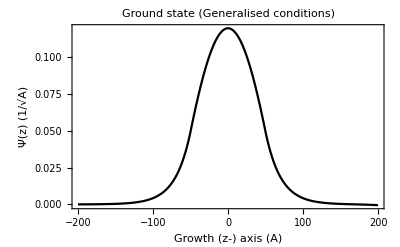

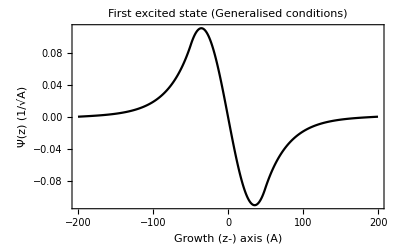

-Graphics-

-Graphics-

```mathematica
energy⟦{2,3}⟧
plots⟦1⟧
plots⟦2⟧
```

## Effect of barrier length on ground state energy and wavefunction: (Parity condition)

Keeping the well width at 100A and changing the width of the barriers

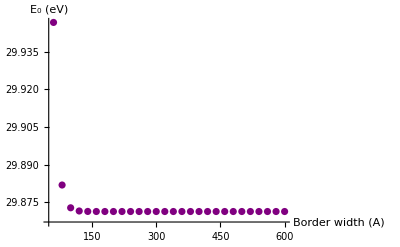

```mathematica
ClearAll["Global`*"]
plots={0.,0.,0.};
titles = {"60 A","200 A", "600 A"};
x=0.2;
plotwidths={60,200,600};n=1;(*n is a counter for the plots(n=1, 60A)(n=2, 200A)(n=3, 600A)*)
hom=7.62559/0.067;(*ℏ^2/m^* for GaAs in eV A^2*)
vmax=0.67*1.247x; (*Diff in conduction band between GaAs and Subscript[Ga, 1-x] Subscript[Al, x] As*)
dz=1.;well = 100;
bw=Range[60,600,20]; (*width of the barrier*)
energy=0.0 bw;
(*Do loop over different border widths*)
Do[
zmax=well/2+bw⟦k⟧;zmin=-zmax;
z=Range[zmin,zmax,dz];lz=Length[z];i0=(Length[z]+1.)/2.;
ψ=0.*z;
v=ConstantArray[vmax,Length[z]];
Do[If[z⟦i⟧-z⟦1⟧>bw⟦k⟧&&z⟦-1⟧-z⟦i⟧>bw⟦k⟧,v⟦i⟧=0.],{i,1,Length[z]}];
c=-0.5*hom/dz^2;b=hom/dz^2+v;
ψmax=2;

ϵ=0.0;dϵ=0.03;
ψ=0.*z;
ψ⟦{i0,i0+1}⟧= {1.,1.+dz^2/hom (v⟦i0⟧-ϵ)} ;
(*Calculating the wavefucntion at zero energy*)
i=i0+1;ψl=ψ⟦i⟧;
While[Abs[ψ⟦i⟧]<ψmax&&i<lz,ψ⟦i+1⟧=1/c (ϵ-b⟦i⟧)ψ⟦i⟧-ψ⟦i-1⟧;i++];
ψl=ψ⟦i⟧;ϵ+=dϵ;

While[Abs[dϵ]>10^-10,
ψ=0.*z;ψ⟦{i0,i0+1}⟧= {1.,1.+dz^2/hom (v⟦i0⟧-ϵ)};
i=i0+1;
While[Abs[ψ⟦i⟧]<ψmax&&i<lz,
ψ⟦i+1⟧=1/c (ϵ-b⟦i⟧)ψ⟦i⟧-ψ⟦i-1⟧;
ψ⟦lz-i+1⟧=ψ⟦i+1⟧;i++];
If[ψ⟦i⟧*ψl<0,dϵ=-dϵ/2.];
ψl=ψ⟦i⟧;ϵ+=dϵ];
(*Selecting three barrier widths with MemberQ to use for plotting*)
If[MemberQ[plotwidths,bw⟦k⟧],
ψ=ψ/(√(ψ.ψ dz));
plots⟦n⟧=ListLinePlot[Table[{z⟦i⟧,ψ⟦i⟧},{i,1,lz}],PlotStyle->Black,Frame->True, FrameLabel->{"Growth (z-) axis (A)","Ψ(z) (1/√A)"},PlotLabel->titles⟦n⟧,PlotRange->All]
;n++];
energy⟦k⟧=ϵ-dϵ;(*dϵ is subtracted to account for a final dϵ added while exiting the while loop*)
,{k,Length[bw]}]
ListPlot[Table[{bw⟦i⟧,1000*energy⟦i⟧},{i,Length[energy]}],PlotStyle->Purple,AxesLabel->{"Border width (A)","E_0 (eV)"},PlotRange->All]
```

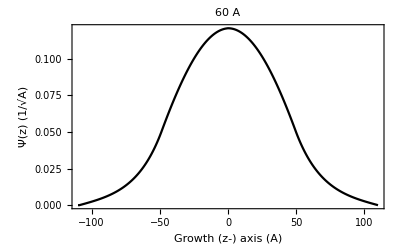

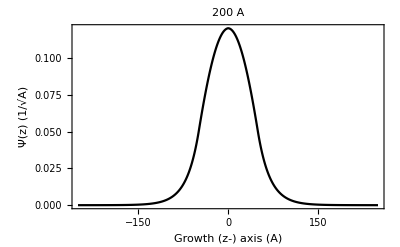

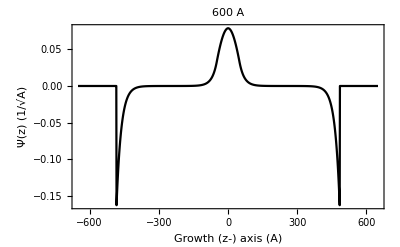

```mathematica
plots⟦1⟧
plots⟦2⟧
plots⟦3⟧
```

## Effect of barrier length on ground state energy and wavefunction: (Generalized condition)

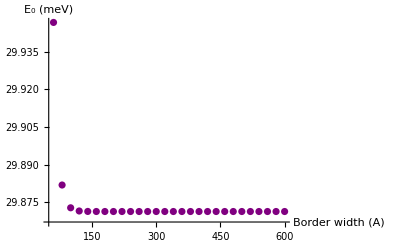

```mathematica
ClearAll["Global`*"]
x=0.2;
plotwidths={60,200,600};n=1;(*n is a counter for the plots(n=1, 60A)(n=2, 200A)(n=3, 600A)*)
plots={0.,0.,0.};
titles = {"60 A","200 A", "600 A"};
hom=7.62559/0.067;(*ℏ^2/m^* for GaAs in eV A^2*)
vmax=0.67*1.247x; (*Diff in conduction band between GaAs and Subscript[Ga, 1-x] Subscript[Al, x] As*)
dz=1.;well = 100;
bw=Range[60,600,20]; (*width of the barrier*)
energy=0.0 bw;
(*Do loop over different border widths*)
Do[
zmax=well/2+bw⟦k⟧;zmin=-zmax;
z=Range[zmin,zmax,dz];lz=Length[z];i0=(Length[z]+1.)/2.;
ψ=0.*z;
v=ConstantArray[vmax,Length[z]];
Do[If[z⟦i⟧-z⟦1⟧>bw⟦k⟧&&z⟦-1⟧-z⟦i⟧>bw⟦k⟧,v⟦i⟧=0.],{i,1,Length[z]}];
c=-0.5*hom/dz^2;b=hom/dz^2+v;
ψmax=2;

ϵ=0.0;dϵ=0.03;
ψ=0.*z;
ψ⟦{i0,i0+1}⟧= {1.,1.+dz^2/hom (v⟦i0⟧-ϵ)} ;
(*Calculating the wavefucntion at zero energy*)
i=i0+1;ψl=ψ⟦i⟧;
While[Abs[ψ⟦i⟧]<ψmax&&i<lz,ψ⟦i+1⟧=1/c (ϵ-b⟦i⟧)ψ⟦i⟧-ψ⟦i-1⟧;i++];
ψl=ψ⟦i⟧;ϵ+=dϵ;

While[Abs[dϵ]>10^-10,
ψ=0.*z;ψ⟦{i0,i0+1}⟧= {1.,1.+dz^2/hom (v⟦i0⟧-ϵ)} ;
i=i0+1;
While[Abs[ψ⟦i⟧]<ψmax&&i<lz,
ψ⟦i+1⟧=1/c (ϵ-b⟦i⟧)ψ⟦i⟧-ψ⟦i-1⟧;
ψ⟦lz-i+1⟧=ψ⟦i+1⟧;i++];
If[ψ⟦i⟧*ψl<0,dϵ=-dϵ/2.];
ψl=ψ⟦i⟧;ϵ+=dϵ];
(*Selecting three barrier widths with MemberQ to use for plotting*)
If[MemberQ[plotwidths,bw⟦k⟧],
ψ=ψ/(√(ψ.ψ dz));
plots⟦n⟧=ListLinePlot[Table[{z⟦i⟧,ψ⟦i⟧},{i,1,lz}],PlotStyle->Black,Frame->True, FrameLabel->{"Growth (z-) axis (A)","Ψ(z) (1/√A)"},PlotLabel->titles⟦n⟧,PlotRange->All]
;n++];

energy⟦k⟧=ϵ-dϵ;(*dϵ is subtracted to account for a final dϵ added while exiting the while loop*)
,{k,Length[bw]}];
ListPlot[Table[{bw⟦i⟧,1000*energy⟦i⟧},{i,Length[energy]}],PlotStyle->Purple,AxesLabel->{"Border width (A)","E_0 (meV)"},PlotRange->All]
```

```mathematica
plots⟦1⟧
plots⟦2⟧
plots⟦3⟧
```

-Graphics-

-Graphics-

-Graphics-